```mathematica
k[n_]:= (π n)/(2L)
1/L Integrate[x Sin[k[i] x]Cos[k[j] x], {x, -L, L}] /. Sin[k[i] L] -> 0 /. Cos[k[j] L] -> 0
```

```mathematica
FullSimplify[-(16 i j L Cos[(i π)/2] Sin[(j π)/2])/((i-j)^2 (i+j)^2 π^2)]
```

```mathematica
L=.; h=.; m=.;
```

```mathematica
const := (h^2 π^2)/(8 m L^2)
```

```mathematica
bigk = 50
```

50

```mathematica
b[5,5]
```

```mathematica
b[i_/;EvenQ[i], j_/;EvenQ[j]]:= 
(- 32 I^(i+j+1) h)/π^2 Sum[ (Exp[I const(i^2 - (2k+1)^2)t] ((2k+1)^2 - j^2) - Exp[I const ((2k+1)^2 - j^2) t] (i^2 - (2k+1)^2))(i(2k+1)^2 j)/((i^2 - (2k+1)^2)^2 ((2k+1)^2 - j^2)^2),{k, 0, bigk}]
b[i_/;OddQ[i], j_/;OddQ[j]]:= 
(32 I^(i+j+1) h)/π^2 Sum[ (Exp[I const(i^2 - (2k)^2)t] ((2k)^2 - j^2) - Exp[I const ((2k)^2 - j^2) t] (i^2 - (2k)^2))(i (2k)^2 j)/((i^2 - (2k)^2)^2 ((2k)^2 - j^2)^2),{k, 1, bigk}]
b[_,_] := 0
```

```mathematica
bigkimp[i_,j_] := i+j;
bimp[i_/;EvenQ[i], j_/;EvenQ[j]]:= 
(- 32 I^(i+j+1) h)/π^2 Sum[ (Exp[I const(i^2 - (2k+1)^2)t] ((2k+1)^2 - j^2) - Exp[I const ((2k+1)^2 - j^2) t] (i^2 - (2k+1)^2))(i(2k+1)^2 j)/((i^2 - (2k+1)^2)^2 ((2k+1)^2 - j^2)^2),{k, 0, bigkimp[i,j]}]
bimp[i_/;OddQ[i], j_/;OddQ[j]]:= 
(32 I^(i+j+1) h)/π^2 Sum[ (Exp[I const(i^2 - (2k)^2)t] ((2k)^2 - j^2) - Exp[I const ((2k)^2 - j^2) t] (i^2 - (2k)^2))(i (2k)^2 j)/((i^2 - (2k)^2)^2 ((2k)^2 - j^2)^2),{k, 1, bigkimp[i,j]}]
bimp[_,_] := 0
```

```mathematica
h = 1; m = 1/2; L = 1/2;
```

```mathematica
bigk =400;
Table[
(I/h N[b[i,j]] - KroneckerDelta[i,j])/t^(1.5)/. t ->00.00001
,{i,1,20},{j,1,20}]//MatrixForm
```

(-83.9956+0. ⅈ | 0.+0. ⅈ | 251.967-0.059682 ⅈ | 0.+0. ⅈ | -419.878+0.298354 ⅈ | 0.+0. ⅈ | 587.689-0.835155 ⅈ | 0.+0. ⅈ | -755.36+1.78894 ⅈ | 0.+0. ⅈ | 922.847-3.27817 ⅈ | 0.+0. ⅈ | -1090.11+5.42077 ⅈ | 0.+0. ⅈ | 1257.1-8.33405 ⅈ | 0.+0. ⅈ | -1423.78+12.1345 ⅈ | 0.+0. ⅈ | 1590.09-16.9378 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -335.962+0. ⅈ | 0.+0. ⅈ | 671.843-0.238699 ⅈ | 0.+0. ⅈ | -1007.57+0.954571 ⅈ | 0.+0. ⅈ | 1343.05-2.38564 ⅈ | 0.+0. ⅈ | -1678.2+4.76925 ⅈ | 0.+0. ⅈ | 2012.95-8.34181 ⅈ | 0.+0. ⅈ | -2347.21+13.3386 ⅈ | 0.+0. ⅈ | 2680.88-19.9935 ⅈ | 0.+0. ⅈ | -3013.87+28.5386 ⅈ | 0.+0. ⅈ | 3346.08-39.2043 ⅈ
251.967+0.059682 ⅈ | 0.+0. ⅈ | -755.841+0. ⅈ | 0.+0. ⅈ | 1259.54-0.596652 ⅈ | 0.+0. ⅈ | -1762.93+2.08769 ⅈ | 0.+0. ⅈ | 2265.9-4.82969 ⅈ | 0.+0. ⅈ | -2768.33+9.17801 ⅈ | 0.+0. ⅈ | 3270.07-15.4865 ⅈ | 0.+0. ⅈ | -3771.01+24.107 ⅈ | 0.+0. ⅈ | 4271.01-35.3892 ⅈ | 0.+0. ⅈ | -4769.91+49.6798 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 671.843+0.238699 ⅈ | 0.+0. ⅈ | -1343.53+0. ⅈ | 0.+0. ⅈ | 2014.89-1.19305 ⅈ | 0.+0. ⅈ | -2685.78+3.81649 ⅈ | 0.+0. ⅈ | 3356.02-8.34501 ⅈ | 0.+0. ⅈ | -4025.44+15.2515 ⅈ | 0.+0. ⅈ | 4693.88-25.0064 ⅈ | 0.+0. ⅈ | -5361.15+38.0776 ⅈ | 0.+0. ⅈ | 6027.06-54.9294 ⅈ | 0.+0. ⅈ | -6691.42+76.0223 ⅈ
-419.878-0.298354 ⅈ | 0.+0. ⅈ | 1259.54+0.596652 ⅈ | 0.+0. ⅈ | -2098.89+0. ⅈ | 0.+0. ⅈ | 2937.76-2.0873 ⅈ | 0.+0. ⅈ | -3775.91+6.25954 ⅈ | 0.+0. ⅈ | 4613.16-13.109 ⅈ | 0.+0. ⅈ | -5449.28+23.2254 ⅈ | 0.+0. ⅈ | 6284.06-37.1953 ⅈ | 0.+0. ⅈ | -7117.27+55.6014 ⅈ | 0.+0. ⅈ | 7948.66-79.0217 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1007.57-0.954571 ⅈ | 0.+0. ⅈ | 2014.89+1.19305 ⅈ | 0.+0. ⅈ | -3021.74+0. ⅈ | 0.+0. ⅈ | 4027.88-3.33865 ⅈ | 0.+0. ⅈ | -5033.04+9.53493 ⅈ | 0.+0. ⅈ | 6036.99-19.2982 ⅈ | 0.+0. ⅈ | -7039.46+33.3342 ⅈ | 0.+0. ⅈ | 8040.19-52.3447 ⅈ | 0.+0. ⅈ | -9038.89+77.0262 ⅈ | 0.+0. ⅈ | 10035.3-108.07 ⅈ
587.689+0.835155 ⅈ | 0.+0. ⅈ | -1762.93-2.08769 ⅈ | 0.+0. ⅈ | 2937.76+2.0873 ⅈ | 0.+0. ⅈ | -4111.88+0. ⅈ | 0.+0. ⅈ | 5285.04-5.00622 ⅈ | 0.+0. ⅈ | -6456.92+13.7606 ⅈ | 0.+0. ⅈ | 7627.23-27.0888 ⅈ | 0.+0. ⅈ | -8795.67+45.8119 ⅈ | 0.+0. ⅈ | 9961.91-70.7459 ⅈ | 0.+0. ⅈ | -11125.6+102.7 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1343.05+2.38564 ⅈ | 0.+0. ⅈ | -2685.78-3.81649 ⅈ | 0.+0. ⅈ | 4027.88+3.33865 ⅈ | 0.+0. ⅈ | -5369.02+0. ⅈ | 0.+0. ⅈ | 6708.88-7.14886 ⅈ | 0.+0. ⅈ | -8047.13+19.0537 ⅈ | 0.+0. ⅈ | 9383.42-36.6557 ⅈ | 0.+0. ⅈ | -10717.4+60.8905 ⅈ | 0.+0. ⅈ | 12048.7-92.687 ⅈ | 0.+0. ⅈ | -13376.9+132.967 ⅈ
-755.36-1.78894 ⅈ | 0.+0. ⅈ | 2265.9+4.82969 ⅈ | 0.+0. ⅈ | -3775.91-6.25954 ⅈ | 0.+0. ⅈ | 5285.04+5.00622 ⅈ | 0.+0. ⅈ | -6792.9+0. ⅈ | 0.+0. ⅈ | 8299.15-9.82533 ⅈ | 0.+0. ⅈ | -9803.39+25.5313 ⅈ | 0.+0. ⅈ | 11305.2-48.1739 ⅈ | 0.+0. ⅈ | -12804.3+78.8021 ⅈ | 0.+0. ⅈ | 14300.1-118.457 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1678.2-4.76925 ⅈ | 0.+0. ⅈ | 3356.02+8.34501 ⅈ | 0.+0. ⅈ | -5033.04-9.53493 ⅈ | 0.+0. ⅈ | 6708.88+7.14886 ⅈ | 0.+0. ⅈ | -8383.13+0. ⅈ | 0.+0. ⅈ | 10055.4-13.0939 ⅈ | 0.+0. ⅈ | -11725.2+33.3094 ⅈ | 0.+0. ⅈ | 13392.1-61.8162 ⅈ | 0.+0. ⅈ | -15055.7+99.7755 ⅈ | 0.+0. ⅈ | 16715.5-148.339 ⅈ
922.847+3.27817 ⅈ | 0.+0. ⅈ | -2768.33-9.17801 ⅈ | 0.+0. ⅈ | 4613.16+13.109 ⅈ | 0.+0. ⅈ | -6456.92-13.7606 ⅈ | 0.+0. ⅈ | 8299.15+9.82533 ⅈ | 0.+0. ⅈ | -10139.4+0. ⅈ | 0.+0. ⅈ | 11977.2-17.0129 ⅈ | 0.+0. ⅈ | -13812.2+42.5041 ⅈ | 0.+0. ⅈ | 15643.7-77.7559 ⅈ | 0.+0. ⅈ | -17471.3+124.041 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 2012.95+8.34181 ⅈ | 0.+0. ⅈ | -4025.44-15.2515 ⅈ | 0.+0. ⅈ | 6036.99+19.2982 ⅈ | 0.+0. ⅈ | -8047.13-19.0537 ⅈ | 0.+0. ⅈ | 10055.4+13.0939 ⅈ | 0.+0. ⅈ | -12061.2+0. ⅈ | 0.+0. ⅈ | 14064.2-21.64 ⅈ | 0.+0. ⅈ | -16063.7+53.2298 ⅈ | 0.+0. ⅈ | 18059.2-96.1633 ⅈ | 0.+0. ⅈ | -20050.2+151.823 ⅈ
-1090.11-5.42077 ⅈ | 0.+0. ⅈ | 3270.07+15.4865 ⅈ | 0.+0. ⅈ | -5449.28-23.2254 ⅈ | 0.+0. ⅈ | 7627.23+27.0888 ⅈ | 0.+0. ⅈ | -9803.39-25.5313 ⅈ | 0.+0. ⅈ | 11977.2+17.0129 ⅈ | 0.+0. ⅈ | -14148.2+0. ⅈ | 0.+0. ⅈ | 16315.8-27.0329 ⅈ | 0.+0. ⅈ | -18479.4+65.6016 ⅈ | 0.+0. ⅈ | 20638.4-117.21 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -2347.21-13.3386 ⅈ | 0.+0. ⅈ | 4693.88+25.0064 ⅈ | 0.+0. ⅈ | -7039.46-33.3342 ⅈ | 0.+0. ⅈ | 9383.42+36.6557 ⅈ | 0.+0. ⅈ | -11725.2-33.3094 ⅈ | 0.+0. ⅈ | 14064.2+21.64 ⅈ | 0.+0. ⅈ | -16399.8+0. ⅈ | 0.+0. ⅈ | 18731.5-33.2485 ⅈ | 0.+0. ⅈ | -21058.5+79.7319 ⅈ | 0.+0. ⅈ | 23380.3-141.063 ⅈ
1257.1+8.33405 ⅈ | 0.+0. ⅈ | -3771.01-24.107 ⅈ | 0.+0. ⅈ | 6284.06+37.1953 ⅈ | 0.+0. ⅈ | -8795.67-45.8119 ⅈ | 0.+0. ⅈ | 11305.2+48.1739 ⅈ | 0.+0. ⅈ | -13812.2-42.5041 ⅈ | 0.+0. ⅈ | 16315.8+27.0329 ⅈ | 0.+0. ⅈ | -18815.6+0. ⅈ | 0.+0. ⅈ | 21310.8-40.3438 ⅈ | 0.+0. ⅈ | -23800.7+95.7346 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 2680.88+19.9935 ⅈ | 0.+0. ⅈ | -5361.15-38.0776 ⅈ | 0.+0. ⅈ | 8040.19+52.3447 ⅈ | 0.+0. ⅈ | -10717.4-60.8905 ⅈ | 0.+0. ⅈ | 13392.1+61.8162 ⅈ | 0.+0. ⅈ | -16063.7-53.2298 ⅈ | 0.+0. ⅈ | 18731.5+33.2485 ⅈ | 0.+0. ⅈ | -21394.8+0. ⅈ | 0.+0. ⅈ | 24052.9-48.3748 ⅈ | 0.+0. ⅈ | -26705.+113.72 ⅈ
-1423.78-12.1345 ⅈ | 0.+0. ⅈ | 4271.01+35.3892 ⅈ | 0.+0. ⅈ | -7117.27-55.6014 ⅈ | 0.+0. ⅈ | 9961.91+70.7459 ⅈ | 0.+0. ⅈ | -12804.3-78.8021 ⅈ | 0.+0. ⅈ | 15643.7+77.7559 ⅈ | 0.+0. ⅈ | -18479.4-65.6016 ⅈ | 0.+0. ⅈ | 21310.8+40.3438 ⅈ | 0.+0. ⅈ | -24137.+0. ⅈ | 0.+0. ⅈ | 26957.4-57.3979 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -3013.87-28.5386 ⅈ | 0.+0. ⅈ | 6027.06+54.9294 ⅈ | 0.+0. ⅈ | -9038.89-77.0262 ⅈ | 0.+0. ⅈ | 12048.7+92.687 ⅈ | 0.+0. ⅈ | -15055.7-99.7755 ⅈ | 0.+0. ⅈ | 18059.2+96.1633 ⅈ | 0.+0. ⅈ | -21058.5-79.7319 ⅈ | 0.+0. ⅈ | 24052.9+48.3748 ⅈ | 0.+0. ⅈ | -27041.4+0. ⅈ | 0.+0. ⅈ | 30023.3-67.4678 ⅈ
1590.09+16.9378 ⅈ | 0.+0. ⅈ | -4769.91-49.6798 ⅈ | 0.+0. ⅈ | 7948.66+79.0217 ⅈ | 0.+0. ⅈ | -11125.6-102.7 ⅈ | 0.+0. ⅈ | 14300.1+118.457 ⅈ | 0.+0. ⅈ | -17471.3-124.041 ⅈ | 0.+0. ⅈ | 20638.4+117.21 ⅈ | 0.+0. ⅈ | -23800.7-95.7346 ⅈ | 0.+0. ⅈ | 26957.4+57.3979 ⅈ | 0.+0. ⅈ | -30107.5+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 3346.08+39.2043 ⅈ | 0.+0. ⅈ | -6691.42-76.0223 ⅈ | 0.+0. ⅈ | 10035.3+108.07 ⅈ | 0.+0. ⅈ | -13376.9-132.967 ⅈ | 0.+0. ⅈ | 16715.5+148.339 ⅈ | 0.+0. ⅈ | -20050.2-151.823 ⅈ | 0.+0. ⅈ | 23380.3+141.063 ⅈ | 0.+0. ⅈ | -26705.-113.72 ⅈ | 0.+0. ⅈ | 30023.3+67.4678 ⅈ | 0.+0. ⅈ | -33334.3+0. ⅈ)

```mathematica
bigk = 80
```

80

```mathematica
n = 5;
(btable = Table[
I/h N[b[i,j]] /. t -> 1/(2^n)
,{i,1,50},{j,1,50}]);
Nest[#.#&, btable, n][[;;10,;;10]]// MatrixForm
```

(1.29878×10^49+0. ⅈ | 0.+0. ⅈ | -4.25291×10^49-3.73265×10^49 ⅈ | 0.+0. ⅈ | 3.61904×10^49+1.12773×10^50 ⅈ | 0.+0. ⅈ | -4.14355×10^49-8.57879×10^49 ⅈ | 0.+0. ⅈ | 5.53443×10^49-2.29511×10^49 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 4.35554×10^49+0. ⅈ | 0.+0. ⅈ | -3.42028×10^49+1.34691×10^50 ⅈ | 0.+0. ⅈ | 9.56399×10^49-2.27654×10^50 ⅈ | 0.+0. ⅈ | -2.9371×10^50+9.30131×10^49 ⅈ | 0.+0. ⅈ | 3.06227×10^50+3.86539×10^49 ⅈ
-4.25291×10^49+3.73265×10^49 ⅈ | 0.+0. ⅈ | 2.47121×10^50+0. ⅈ | 0.+0. ⅈ | -4.44009×10^50-2.65885×10^50 ⅈ | 0.+0. ⅈ | 3.83681×10^50+1.61742×10^50 ⅈ | 0.+0. ⅈ | -1.14838×10^50+2.34008×10^50 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -3.42028×10^49-1.34691×10^50 ⅈ | 0.+0. ⅈ | 6.38933×10^50+0. ⅈ | 0.+0. ⅈ | -1.07655×10^51-1.64259×10^50 ⅈ | 0.+0. ⅈ | 5.79274×10^50+1.01595×10^51 ⅈ | 0.+0. ⅈ | 2.50971×10^49-1.09826×10^51 ⅈ
3.61904×10^49-1.12773×10^50 ⅈ | 0.+0. ⅈ | -4.44009×10^50+2.65885×10^50 ⅈ | 0.+0. ⅈ | 1.08409×10^51+0. ⅈ | 0.+0. ⅈ | -8.63717×10^50+1.22389×10^50 ⅈ | 0.+0. ⅈ | -4.58874×10^49-5.43479×10^50 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 9.56399×10^49+2.27654×10^50 ⅈ | 0.+0. ⅈ | -1.07655×10^51+1.64259×10^50 ⅈ | 0.+0. ⅈ | 1.86411×10^51+0. ⅈ | 0.+0. ⅈ | -1.2676×10^51-1.59025×10^51 ⅈ | 0.+0. ⅈ | 2.78032×10^50+1.90296×10^51 ⅈ
-4.14355×10^49+8.57879×10^49 ⅈ | 0.+0. ⅈ | 3.83681×10^50-1.61742×10^50 ⅈ | 0.+0. ⅈ | -8.63717×10^50-1.22389×10^50 ⅈ | 0.+0. ⅈ | 7.04355×10^50+0. ⅈ | 0.+0. ⅈ | -2.52553×10^49+4.38455×10^50 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -2.9371×10^50-9.30131×10^49 ⅈ | 0.+0. ⅈ | 5.79274×10^50-1.01595×10^51 ⅈ | 0.+0. ⅈ | -1.2676×10^51+1.59025×10^51 ⅈ | 0.+0. ⅈ | 2.36712×10^51+0. ⅈ | 0.+0. ⅈ | -2.05272×10^51-1.08835×10^51 ⅈ
5.53443×10^49+2.29511×10^49 ⅈ | 0.+0. ⅈ | -1.14838×10^50-2.34008×10^50 ⅈ | 0.+0. ⅈ | -4.58874×10^49+5.43479×10^50 ⅈ | 0.+0. ⅈ | -2.52553×10^49-4.38455×10^50 ⅈ | 0.+0. ⅈ | 2.77809×10^50+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 3.06227×10^50-3.86539×10^49 ⅈ | 0.+0. ⅈ | 2.50971×10^49+1.09826×10^51 ⅈ | 0.+0. ⅈ | 2.78032×10^50-1.90296×10^51 ⅈ | 0.+0. ⅈ | -2.05272×10^51+1.08835×10^51 ⅈ | 0.+0. ⅈ | 2.38064×10^51+0. ⅈ)

```mathematica
(btable = Table[
I/h N[b[i,j]] /. t -> 1
,{i,1,300},{j,1,300}]);
```

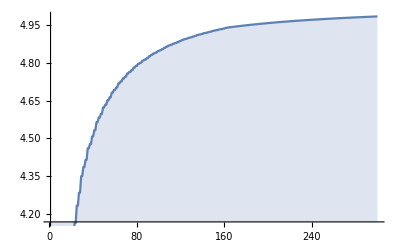

```mathematica
DiscretePlot[{Exp[Norm[btable[[;;i,1]] .btable[[1,;;i]]]^2]}, {i,1,300}]
```

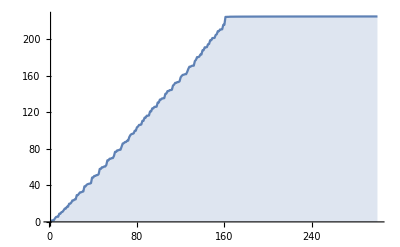

```mathematica
DiscretePlot[Norm@Eigenvalues[btable[[;;i,;;i]] ,1], {i,1,300}]
```

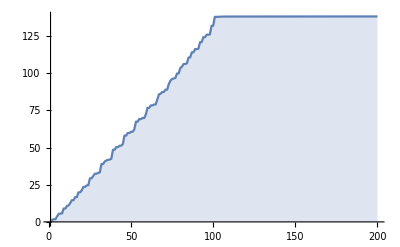

```mathematica
DiscretePlot[Norm@Eigenvalues[btable[[;;i,;;i]] ,1], {i,1,200}]
```

```mathematica
btable[[;;10,;;10]]
```

{{-0.247443+0. ⅈ,0.+0. ⅈ,-0.637063+0.385981 ⅈ,0.+0. ⅈ,0.40895-0.389659 ⅈ,0.+0. ⅈ,0.137871+0.30112 ⅈ,0.+0. ⅈ,0.0333584-0.145863 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.42962+0. ⅈ,0.+0. ⅈ,-0.652147+0.555538 ⅈ,0.+0. ⅈ,-0.894137-0.564874 ⅈ,0.+0. ⅈ,0.513996+0.398399 ⅈ,0.+0. ⅈ,0.0767484-0.0037289 ⅈ},{-0.637063-0.385981 ⅈ,0.+0. ⅈ,1.48943+0. ⅈ,0.+0. ⅈ,1.4713+0.380303 ⅈ,0.+0. ⅈ,-1.33965-0.0102378 ⅈ,0.+0. ⅈ,0.244867-0.395504 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.652147-0.555538 ⅈ,0.+0. ⅈ,-0.271032+0. ⅈ,0.+0. ⅈ,2.60412-0.481461 ⅈ,0.+0. ⅈ,-1.6944-0.0430758 ⅈ,0.+0. ⅈ,0.0832925-0.778874 ⅈ},{0.40895+0.389659 ⅈ,0.+0. ⅈ,1.4713-0.380303 ⅈ,0.+0. ⅈ,-3.16303+0. ⅈ,0.+0. ⅈ,2.7281-0.286856 ⅈ,0.+0. ⅈ,-0.0827144+1.69577 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.894137+0.564874 ⅈ,0.+0. ⅈ,2.60412+0.481461 ⅈ,0.+0. ⅈ,-3.8078+0. ⅈ,0.+0. ⅈ,0.0740624-1.24383 ⅈ,0.+0. ⅈ,2.4301+0.178249 ⅈ},{0.137871-0.30112 ⅈ,0.+0. ⅈ,-1.33965+0.0102378 ⅈ,0.+0. ⅈ,2.7281+0.286856 ⅈ,0.+0. ⅈ,-0.85729+0. ⅈ,0.+0. ⅈ,-4.24745+0.346033 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.513996-0.398399 ⅈ,0.+0. ⅈ,-1.6944+0.0430758 ⅈ,0.+0. ⅈ,0.0740624+1.24383 ⅈ,0.+0. ⅈ,3.42667+0. ⅈ,0.+0. ⅈ,-4.57973+0.204884 ⅈ},{0.0333584+0.145863 ⅈ,0.+0. ⅈ,0.244867+0.395504 ⅈ,0.+0. ⅈ,-0.0827144-1.69577 ⅈ,0.+0. ⅈ,-4.24745-0.346033 ⅈ,0.+0. ⅈ,6.60203+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.0767484+0.0037289 ⅈ,0.+0. ⅈ,0.0832925+0.778874 ⅈ,0.+0. ⅈ,2.4301-0.178249 ⅈ,0.+0. ⅈ,-4.57973-0.204884 ⅈ,0.+0. ⅈ,3.66657+0. ⅈ}}

```mathematica
bigk=600
```

600

```mathematica
Evaluate[bimp[0,2]]
```

0

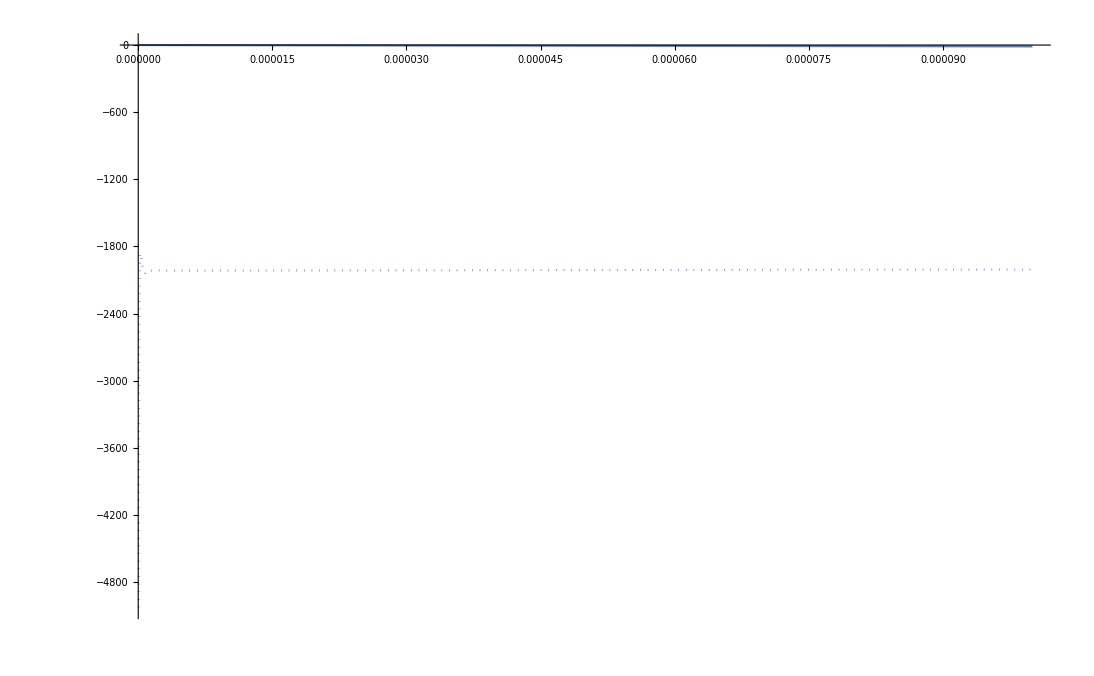

```mathematica
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[4,6]]],
compiledapprox = Compile[{{t,_Real}},Evaluate[bimp[1,1]]]},
ReImPlot[{(compiled[t])/t^(1.5),(*compiledapprox[t]+I*)}, {t, 0, 0.0001}]]
```

```mathematica
b[2,2] /. t -> 1 // N
```

```mathematica
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[2,2]]],
compiledapprox = Compile[{{t,_Real}}, Evaluate[Block[{bigk = 1}, b[2,2]]]]},
ReImPlot[{compiled[t],compiledapprox[t]}, {t, 0, 5}]]
```

```mathematica
bigk=30
```

```mathematica
Table[
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[i,j]]],
compiledapprox = Compile[{{t,_Real}}, Evaluate[bimp[i,j]]]},
ReImPlot[{compiled[t],compiledapprox[t]}, {t, 0, 1}]], {i,1, 26},{j,1,2}] // TableForm
```

```mathematica
Table[
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[i,j]]],
compiledapprox = Compile[{{t,_Real}}, Evaluate[Block[{bigk = 3}, b[i,j]]]]},
ReImPlot[{compiled[t],compiledapprox[t]}, {t, 0, 1}]], {i, 1, 8},{j,1,8}] // TableForm
```

```mathematica
bigk = 1
```

```mathematica
Table[
Module[{compiled = Compile[{{t,_Real}}, Evaluate[b[i,j]]]},
ReImPlot[compiled[t], {t, 0, 5}]], {i, 0, 8},{j,0,8}] // TableForm
```

```mathematica
comp[0.2]
```

```mathematica
ReImPlot[comp[t], {t, 0, 5}]
```

```mathematica
bigk = 100
```

```mathematica
c2[n_]:= Sum[-b[n,k]b[k,n], {k, 0, bigk}];
expr1 = Compile[{t}, Evaluate[c2[1]]]
expr2 = Compile[{t}, Evaluate[c2[2]]]
expr5 = Compile[{t}, Evaluate[c2[5]]]
expr10 = Compile[{t}, Evaluate[c2[10]]]
LogPlot[{expr1[t], expr2[t], expr5[t], expr10[t]}, {t, 0, 1}]
```

```mathematica
c2[n_]:= Sum[-b[n,k]b[k,n], {k, 0, bigk}];
expr1 = Compile[{t}, Evaluate[c2[5]]]
expr2 = Compile[{t},  Evaluate[-b[5,5]^2]]
ReImPlot[{expr1[t],expr2[t]}, {t, 0, 1}]
```

```mathematica
bigk = 30
```

```mathematica
c2[n_]:= Sum[-b[n,k1]b[k1,k2]b[k2,n], {k1, 0, bigk}, {k2, 0, bigk}];
expr = Compile[{t}, Evaluate[c2[3]]]
ReImPlot[{expr[t], -b[3,3]^3}, {t, 0, 0.1}]
```

```mathematica
c2[n_]:= Sum[-b[n,k1]b[k1,k2]b[k2,k3]b[k3,n], {k1, 0, bigk}, {k2, 0, bigk}, {k3,0,bigk}];
expr = Compile[{t}, Evaluate[c2[1]]]
ReImPlot[{expr[t], -b[1,1]^4}, {t, 0, 0.01}]
```

```mathematica
bigk=3
```

```mathematica
c2[n_]:= Sum[-b[n,k1]b[k1,k2]b[k2,k3]b[k3,k4]b[k4,k5] b[k5,n], {k1, 0, bigk}, {k2, 0, bigk}, {k3,0,bigk}, {k4,0,bigk}, {k5,0,bigk}];
expr = Compile[{t}, Evaluate[FullSimplify[c2[1]]]]
ReImPlot[{expr[t]}, {t, 0, 1}]
```

```mathematica
v0=.
v0 = v0 /.First@Solve[qf == q0 + v0 tf - 1/2 k tf^2/m, v0]
```

```mathematica
Integrate[1/2 m (v0  -  k t/m)^2 - k ( v0 t - 1/2 k t^2/m) + V0, {t, 0, tf}] // FullSimplify
```

```mathematica
K[q0_, qf_, t_] := Sqrt[m/(2 I π h t)] Exp[I/h((m (q0-qf)^2)/(2 t)+1/2 V'[q0] (q0-qf) t-(V'[q0]^2 t^3)/(24 m)+t V[q0])]
```

```mathematica
K[q0,qf,t] /. V -> Function[x,0]
```

```mathematica
integrand = - I h y D[K[y,x,-eps],x] K[qf, y, eps] /. V -> Function[x, U[qf] + U'[qf] (x - qf)]
```

```mathematica
integrand = - I h  D[K[x,y,eps],x] K[y,qf,eps] /. V -> Function[x,0]// FullSimplify
```

```mathematica
ReImPlot[integrand /. m -> 1 /. eps -> 1 /. h ->1 /. x -> 1 /. qf -> 0 /. U -> Function[x,x^2], {y, -1,30}]
```

```mathematica
integrand /. m -> 1 /. eps -> 1 /. h ->1 /. x -> 2 /. qf -> 0 /. V -> Function[x,x^4] /. y -> 1
```

```mathematica
integrand /. m -> 1 /. eps -> 1 /. h ->1 /. x -> 2 /. qf -> 0 /. V -> Function[x,x^2]
```

```mathematica
Integrate[V -> Function[x,x^4]/. m -> 1 /. eps -> eps /. h ->1  /. qf -> 0 ,{y,-∞,∞}]
```

```mathematica
ReImPlot[-(3 ⅇ^(-(ⅈ (3-6 eps^2+4 eps^4) x^2)/(2 eps^3 (-12+eps^2))) √(1/eps^2) √(-ⅈ eps (-12+eps^2)) (1+eps^2) √(3/(2 π)) (eps^3 (-12+eps^2)-ⅈ (3-6 eps^2+4 eps^4) x^2))/(eps^6 (-12+eps^2)^3) /. x -> 2, {eps, 0, 10}]
```

```mathematica
NIntegrate[eps integrand /. m -> 1 /. eps -> 0.01 /. h ->1 /. x -> 2 /. qf -> 0 /. U -> Function[x,x^2], {y, 100,200}]
```

```mathematica
ReImPlot[Abs@NIntegrate[eps integrand /. m -> 1/. h ->1 /. x -> 2 /. qf -> 0 /. U -> Function[x,x^2], {y, -200,200}], {eps, 0, 1}]
```